I want to see if there is a method to extract the peaks from a nerve that has multiple frequencies and components.
This is the limiting factor in Marcos’ current version of his stream analysis (as of 23.01.2025) which is why we have been using special ratios where the 
DP converge such as f2/f1=1.5 which yield cleaner results.

```mathematica
Clear[findMinima]
findMinima[fftValues_,sampleSize_:4000,sRate_:20000]:=Block[{freq,amp,phase,period},
(* predicts where the minima of a Cosine would appear depending on the phase added on it *)
{freq,amp,phase}=fftValues;
period=sRate/freq;
 period((1./2-phase/360)+# )&/@Range[0,sampleSize/sRate freq]
]
```

```mathematica
Clear[findNervePeaks]
Options[findNervePeaks]={
"FFTampThreshold"->0.02,
"peakSharpness"->0.03,
"ampThreshold"->0.2
};
findNervePeaks[data_,opts:OptionsPattern[{findNervePeaks}]]:=Block[{
FFTampThreshold,ampThreshold,peakSharpness,nerveFFT,
nerveFFTphase,fftPeaksPos,fftPeaks,freqSampleSizes,nervePeakPos,nervePeaks,freqResolution},
(* 
data: accepts a 1D nerve response for a given samplerate sRate.
*)

FFTampThreshold=OptionValue["FFTampThreshold"];
ampThreshold=OptionValue["ampThreshold"];
peakSharpness=OptionValue["peakSharpness"];

(* spectral analysis *);
nerveFFT=fourier[data,sRate,1200]; (*Step 1: take the FFT of the data*)
nerveFFTphase=fourier[data,sRate,1200,FFTampThreshold,"ϕ"][[;;,2]]; (*find the phases of all frequencies involved*)
fftPeaksPos=FindPeaks[nerveFFT[[;;,2]],0.001,Automatic,FFTampThreshold][[;;,1]]; (*Find which frequencies are involved in the nerve data*) 
fftPeaks=Flatten/@({nerveFFT[[fftPeaksPos]],nerveFFTphase[[fftPeaksPos]]}ᵀ); (* extract the frequency, amplitude and phase, for each peak found in the FFT *);
freqSampleSizes=Round[sRate/fftPeaks[[;;,1]]] (* these are the distance between samples that belong in a stream of a particular frequency. 
For example, a 180 Hz stream sampled at 20kHz, would have peaks separated by  about 111 samples.*);
freqResolution=sRate/Length@data;

(*temporal analysis*);

nervePeakPos=FindPeaks[-data,.1,peakSharpness,ampThreshold][[;;,1]]; (* find all the peaks you can find on the temporal level in the nerve *)
nervePeaks={nervePeakPos,data[[nervePeakPos]]}ᵀ (* these are the nerve peaks*);

{fftPeaks,freqSampleSizes,nervePeaks,freqResolution}
]
```

```mathematica
Clear[DiscardCloseElements]

DiscardCloseElements[list_List, minDistance_] := 
  Fold[
    (* Only keep the element if it's at least minDistance away from the last one kept *)
    If[#2 - Last[#] >= minDistance, Append[#, #2], #] &,
    {First[list]}, (* Start with the first element in the list *)
    Rest[list] (* Process the rest *)
  ]

Clear[errorThreshold]
errorThreshold[freq_,errorThreshold_:5]:= Round[Abs[1. sRate(1/freq-1/(freq+errorThreshold))]] (* if in a 180 Hz stream, the distance between samples would be ~111. What would it be if we were to allow for an error margin of 5 Hz? *)


Clear[SelectSequence]
SelectSequence[pairs_List]:=Module[{sequence={First[pairs]},currentPair,remainingPairs},
 
(*the purpose of this function is to find streams at their most rudimentary form.
If looking for a stream at a particular frequency, or, in other words, a specific number of samples apart, they form a pair
{{1,5},{3,15},{5,29},...}. In this case, the purpose of the code to "continue the pairs".
The example above, the pairs {1,5} and {5,29} are part of the same stream as one continues from where the previous one stopped.*)

(*Initialize the current pair and the remaining pairs*)currentPair=First[pairs];
remainingPairs=Rest[pairs];
(*Build the sequence iteratively*)While[remainingPairs=!={},(*Find the next pair where the first element matches the last element of the current pair*)
currentPair=SelectFirst[remainingPairs,#[[1]]==Last[sequence[[-1]]]&,None];
If[currentPair===None,(*Stop if no matching pair is found*)Break[],
(*Add the matching pair to the sequence and remove it from the list*)AppendTo[sequence,currentPair];
remainingPairs=DeleteCases[remainingPairs,currentPair]];];
Union@Flatten[sequence]]


Clear[removeSubsets]
removeSubsets[data_]:=Block[{listOfStreams,streams,currentStream,remainingStreams},
(* in finding streams, one will inevitable find subsets of a larger stream.
For instance, if a stream was {1,5,23,55,79,98}, then the code is likely to also find {5,23,55,79,98}
and {23,55,79,98}, etc..
This code's role is to iteratively eliminate such subsets
*)

listOfStreams=Reverse[SortBy[data,Length]] (* sort the streams by largest *);

If[ listOfStreams=={},{},
streams={First@listOfStreams} (* the stream is defined by at least the largest stream we can find *);
remainingStreams=Rest[listOfStreams] (* the remaining streams are those that are yet to be inspected *);

Quiet@While[remainingStreams!={},
currentStream=Last[streams];

remainingStreams=Select[remainingStreams,Not@SubsetQ[currentStream,#]&];
If[remainingStreams=={},Break[],
AppendTo[streams,First@remainingStreams];
remainingStreams=DeleteCases[remainingStreams,First@remainingStreams];
](*end of second if *)

](* end of first if*)
];
streams
] (* end of Block *)
```

```mathematica
Round[sRate/180.]
```

111

```mathematica
Options[findNerveStream]={


"minStreamSize"->5,
"cleanClosePeaks"->True,
"peakProximityThreshold"->5 (* corresponds to a frequency component of 20000/5 = 4000 Hz signal which is very unlikely to exist in the nerve*),
"freqResolution"->5};

findNerveStream[data_,targetFrequency_,opts:OptionsPattern[{findNerveStream}]]:=Block[{cleanClosePeaks,peakProximityThreshold,minStreamSize,rawData,freqSampleSizerawData,freqSampleSize,cleanPeaks,streamPairs,streamSegments,freqResolution},
(*
data: accepts the 1D nervePeaks
*)
minStreamSize=OptionValue["minStreamSize"]; (* the minimum size of a stream *);
cleanClosePeaks=OptionValue["cleanClosePeaks"]; (* boolean as to whether to remove peaks identified on the same CAP *);
peakProximityThreshold=OptionValue["peakProximityThreshold"] (* threshold to remove peaks from the same CAP in terms of samples.*); 
freqResolution=OptionValue["freqResolution"];
freqSampleSize=Round[1. sRate/targetFrequency];

rawData=data[[;;,1]];
cleanPeaks=If[cleanClosePeaks,DiscardCloseElements[rawData,peakProximityThreshold],rawData];
streamPairs=Flatten[Table[If[Between[cleanPeaks[[i]]-cleanPeaks[[j]],freqSampleSize+Round@errorThreshold[sRate/freqSampleSize,freqResolution]{-1,1}],
Flatten[Position[rawData,#]&/@{cleanPeaks[[j]],cleanPeaks[[i]]}],Nothing],{j,Length@cleanPeaks},{i,Length@cleanPeaks}],1];

If[streamPairs=={},{},

streamSegments=Select[Table[SelectSequence[streamPairs[[i;;]]],{i,Length@streamPairs}],Length@#>=minStreamSize&];
If[streamSegments=={},{},
data[[#]]&/@removeSubsets[streamSegments]
](* end of 2nd if*)

] (*end of 1st if*)

](* end of Block *)

(*findNerveStream[nervePeaks,freqSampleSizes[[freqSelected]]];*)
```

```mathematica
(*{nfileNames311T,nfileNames312T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};
{lfileNames311T,lfileNames312T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Laser\\healthy_files\\*"<>#<>"*.txt"]&/@{"a","b"};*)
{nervefiles1T,nervefiles2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Nerve\\healthy_files\\*"<>"_"<>#<>"_"<>"*.txt"]&/@{"a","b"};
{lfileNames1T,lfileNames2T}=FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_1\\Laser\\healthy_files\\*"<>"_"<>#<>"_"<>"*.txt"]&/@{"a","b"};
expDuration=4; (* seconds*)
numOfSegments=20; (* the number of segments I want to generate from the TOTAL nerve response - the full experimental duration  *)
sRate=20000;
expSize=expDuration sRate/numOfSegments (* number of samples per segment *);
```

```mathematica
frequencyList=Import[FileNames["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito32\\exp_Config.txt"][[1]],"TSV"][[7;;,2]];
freqMap=AssociationThread[Range[Length@frequencyList],frequencyList](* mapping an experimental number with a frequency*);
freqs1T=freqMap[#]&/@Sort@ToExpression[StringTake[nervefiles1T,{-8,-6}]]; (* frequencies of the one-tone experiments that made it past the health check *)
freqs2T=freqMap[#]&/@Sort@ToExpression[StringTake[nervefiles2T,{-8,-6}]];(* frequencies of the two-tone experiments that made it past the health check *)
```

```mathematica
Flatten[Position[freqs1T,#]&/@{180}]
Flatten[Position[freqs2T,#]&/@{360,720,900}]
```

{9}

{26,60,78}

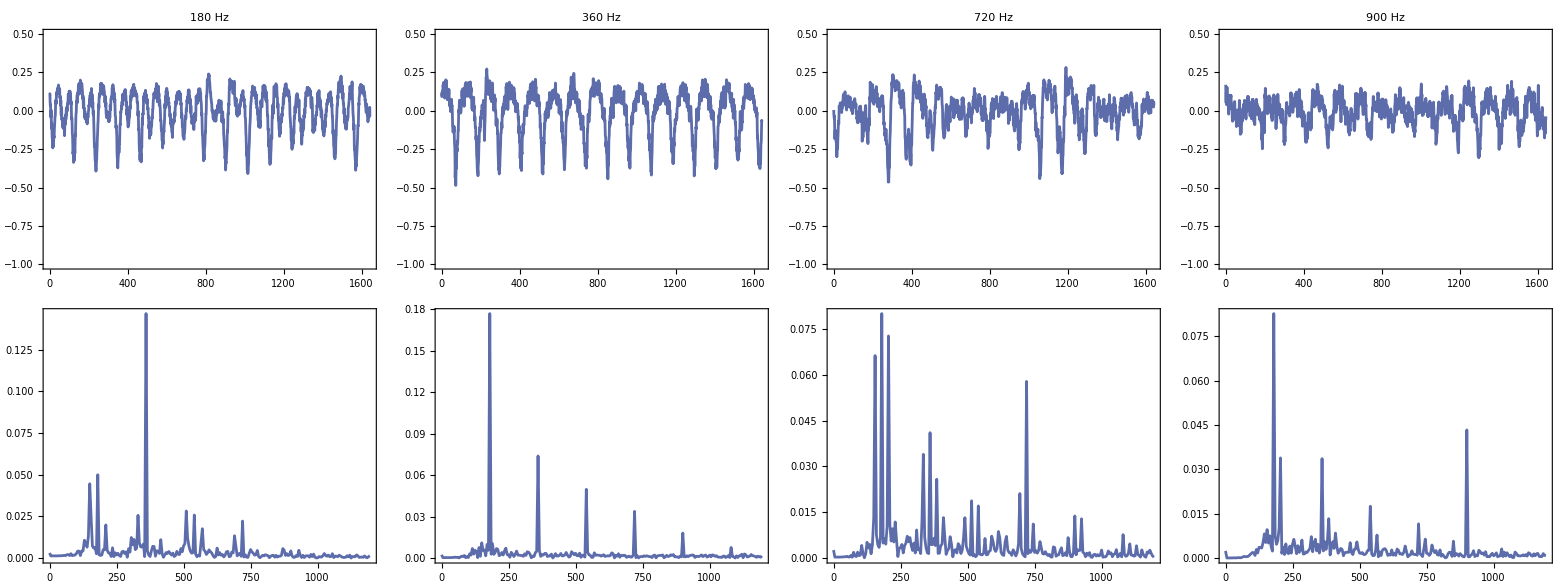

```mathematica
fNerve1T=Fold[HighpassFilter,readMyFile[nervefiles1T[[9]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}];  (* this is for f1=180 Hz, f1 *)
fNerve2T=Fold[HighpassFilter,readMyFile[nervefiles2T[[26]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1 = 360 Hz, f2-f1 *)
fNerve2TQ2=Fold[HighpassFilter,readMyFile[nervefiles2T[[60]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1=720 Hz,  f1-f2 Hz*)
fNerve2TC2=Fold[HighpassFilter,readMyFile[nervefiles2T[[78]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1=900 Hz, 2f2-f1 Hz*)
nerveFile1T=Partition[fNerve1T,expSize]; 
nerveFile2T=Partition[fNerve2T,expSize]; 
nerveFile2TQ2=Partition[fNerve2TQ2,expSize]; 
nerveFile2TC2=Partition[fNerve2TC2,expSize]; 

cleanN1T=cleanTheNerve[nerveFile1T];
cleanN2T=cleanTheNerve[nerveFile2T];
cleanN2TQ2=cleanTheNerve[nerveFile2TQ2];
cleanN2TC2=cleanTheNerve[nerveFile2TC2];
cleanData={cleanN1T,cleanN2T,cleanN2TQ2,cleanN2TC2};

SegChosen=10;
Grid@{MapThread[ListLinePlot[#1[[SegChosen]][[maxTime;;2maxTime]],ImageSize->300,PlotRange->{-1,0.5},PlotLabel->#2<>" Hz"]&,{{cleanN1T,cleanN2T,cleanN2TQ2,cleanN2TC2},{"180","360","720","900"}}],
ListLinePlot[fourier[#[[SegChosen]],sRate,1200],ImageSize->300]&/@{cleanN1T,cleanN2T,cleanN2TQ2,cleanN2TC2}}
```

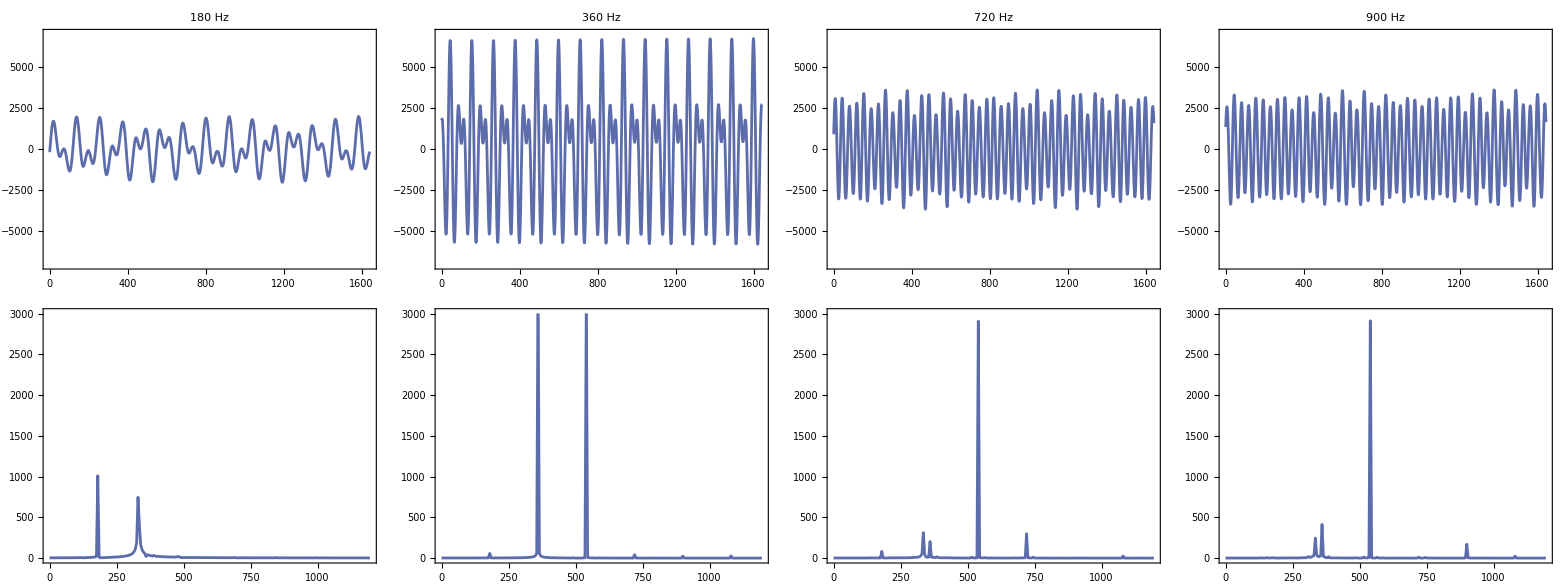

```mathematica
lNerve1T=Fold[HighpassFilter,readMyFile[lfileNames1T[[9]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}];  (* this is for f1=180 Hz, f1 *)
lNerve2T=Fold[HighpassFilter,readMyFile[lfileNames2T[[26]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1 = 360 Hz, f2-f1 *)
lNerve2TQ2=Fold[HighpassFilter,readMyFile[lfileNames2T[[60]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1=720 Hz,  f1-f2 Hz*)
lNerve2TC2=Fold[HighpassFilter,readMyFile[lfileNames2T[[78]]][[;;expDuration sRate,2]],(2π)/sRate{60,60,60,60,60}]; (* this is for f1=900 Hz, 2f2-f1 Hz*)
laserFile1T=Partition[lNerve1T,expSize]; 
laserFile2T=Partition[lNerve2T,expSize]; 
laserFile2TQ2=Partition[lNerve2TQ2,expSize]; 
laserFile2TC2=Partition[lNerve2TC2,expSize]; 

SegChosen=10;
Grid@{MapThread[ListLinePlot[#1[[SegChosen]][[maxTime;;2maxTime]],ImageSize->300,PlotRange->1000{-7,7},PlotLabel->#2<>" Hz"]&,{{laserFile1T,laserFile2T,laserFile2TQ2,laserFile2TC2},{"180","360","720","900"}}],
ListLinePlot[fourier[#[[SegChosen]],sRate,1200],ImageSize->300,PlotRange->{0,3000}]&/@{laserFile1T,laserFile2T,laserFile2TQ2,laserFile2TC2}}
```

So, I will start with the simplest case, which is f1=180 Hz, to see if I can write an algorithm that will find two streams: one at f1 and one at 2f1

```mathematica
findStreams[data_,targetFrequency_,opts:OptionsPattern[{findNervePeaks,findNerveStream}]]:=Block[
{minStreamSize,cleanClosePeaks,peakProximityThreshold,peakSharpness,fftPeaks,freqSampleSizes,nervePeaks,freqResolution,streams},

minStreamSize=OptionValue["minStreamSize"](* the minimum size of a stream *);
cleanClosePeaks=OptionValue["cleanClosePeaks"] (* boolean as to whether to remove peaks identified on the same CAP *);
peakProximityThreshold=OptionValue["peakProximityThreshold"] (* threshold to remove peaks from the same CAP in terms of samples.*); 
freqResolution=OptionValue["freqResolution"];
peakSharpness=OptionValue["peakSharpness"];

{fftPeaks,freqSampleSizes,nervePeaks,freqResolution}=findNervePeaks[data,"peakSharpness"->peakSharpness];
streams=findNerveStream[nervePeaks,targetFrequency,
"cleanClosePeaks"->cleanClosePeaks,"minStreamSize"->minStreamSize,"peakProximityThreshold"->peakProximityThreshold,"freqResolution"->freqResolution];

]
```

{180.,205.,360.,540.}

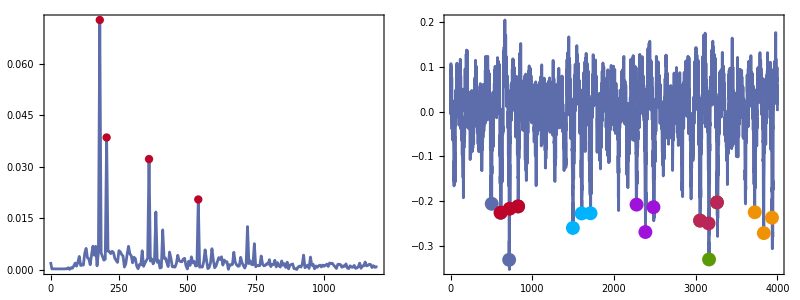

```mathematica
Clear[dataChosen,fftPeaks,freqSampleSizes,nervePeaks,freqResolution]
dataChosen=cleanTheNerve[cleanData[[4]][[8]],900,False];
{fftPeaks,freqSampleSizes,nervePeaks,freqResolution}=findNervePeaks[dataChosen,"peakSharpness"->Automatic];
fftPeaks[[;;,1]] (* these are the frequencies in the nerve*)

streams=findNerveStream[nervePeaks,192,
"cleanClosePeaks"->True,"minStreamSize"->3,"peakProximityThreshold"->5,"freqResolution"->15];
Grid@{{
(*FFT*)
ListLinePlot[fourier[dataChosen,sRate,1200],Epilog->{red,AbsolutePointSize[6],Point[#]&/@fftPeaks[[;;,{1,2}]]}],
(*temporal + streams*)
Show[{ListLinePlot[dataChosen[[;;4000]],ImageSize->800,Epilog->{Black,Opacity[0], Point[#]&/@nervePeaks},AspectRatio->1/4],
(*ListPlot[nervePeaks],*)ListPlot[streams]}]}}
```

```mathematica
1.sRate/Differences[streams[[1,;;,1]]]
```

{173.913,180.18,188.679}

```mathematica
0.0385/0.0728
```

0.528846

```mathematica
1. sRate/Mean[Differences[{2170,2276,2384,2483,2607}]]
```

183.066

```mathematica
1. Mean[{ 360,385,410}]/2
```

192.5

```mathematica
Mean[1.{180,205}]
```

192.5

```mathematica
sRate/114.
```

175.439

```mathematica
Solve[#==270,f1]&/@({f1-f2,2f1-f2,2f2-f1}/.{f2->540})
```

{{{f1→810}},{{f1→405}},{{f1→810}}}

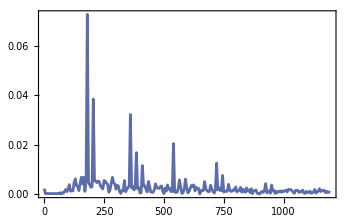

```mathematica
fourier[cleanTheNerve[cleanData[[4]][[8]],900,False],sRate,1200]//ListLinePlot
```

#### LONGEST COMMON SUBSEQUENCE

We can use this to separate subsets.

```mathematica
LongestCommonSubsequence["AAABBBBCCCCC","CCCBBBAAABABA"]
```

AAAB